# Flip-Flop Cavity Coupling

```mathematica
SetDirectory[NotebookDirectory[]];Get["include/Perturbation_Theory.m"];Get["include/Pauli_Elem_Representation.m"];Get["include/Plotting_Definitions.m"];
```

## Numerical Parameters

```mathematica
subDef={Cos[η]-> ϵ/w0,Sin[η]-> Vt/w0,η->ArcTan[ϵ,Vt],w0->√(ϵ^2+Vt^2)};
subNum={λ->1,A->0.117,ΔwB->-0.001999*wB,wrms-> 0.323};
subAll=Join[{δ-> δf-(2 gc^2)/δc,δf-> wf-wcav,δc-> wc-wcav,wf->E1-E0,wc->E2-E0,gc->1/2*g*z10,gf->1/2*g*z31,wxy-> 1/2*wrms*(z11+z22)*gc/δc,wz->1/2 wrms*(z03-z30+z33),Subscript[α, 0,0]->0,Subscript[α, 0,1]->1,Subscript[α, 1,0]->0,Subscript[α, 1,1]->0,Subscript[β, 0]->1/2,Subscript[β, 1]->1/2},subE,subZ,subDef,subNum];
TScale=1000000; (* 1 unit = 1000000 ns = 1ms *)
```

```mathematica
Hbare0=-1/2*w0*KroneckerProduct[PauliMatrix[3],PauliMatrix[0]]-1/2 wB*KroneckerProduct[PauliMatrix[0],PauliMatrix[3]];
HbareA=A/8 KroneckerProduct[PauliMatrix[0]-(Cos[η]*PauliMatrix[3]+Sin[η]*PauliMatrix[1]),2*PauliMatrix[1]-PauliMatrix[0]];
HbareΔ=-1/4 ΔwB*KroneckerProduct[PauliMatrix[0]+(Cos[η]*PauliMatrix[3]+Sin[η]*PauliMatrix[1]),PauliMatrix[3]];
```

```mathematica
(* Determine Flip-Flop Eigenbasis *)
UnperturbedEnergies=Diagonal[Hbare0];
Perturbation=λ*FullSimplify[(HbareA+HbareΔ)];
FlipFlopEnergies=Collect[Expand[Energies[UnperturbedEnergies,Perturbation,2]],{λ}];
FlipFlipStates=Collect[Expand[States[UnperturbedEnergies,Perturbation,2]],{λ}];
subE={E0-> FlipFlopEnergies[[1]],E1-> FlipFlopEnergies[[2]],E2->FlipFlopEnergies[[3]],E3-> FlipFlopEnergies[[4]]};
Z=Normal[Series[Inverse[FlipFlipStates].KroneckerProduct[Cos[η]*PauliMatrix[3]+Sin[η]*PauliMatrix[1],PauliMatrix[0]].FlipFlipStates,{λ,0,2}]];
Zcoef=ArrayReshape[Collect[Expand[Simplify[MatrixToPauli[Z]]],{λ}],{4,4}];
subZ={z01-> Zcoef[[1,2]],z03-> Zcoef[[1,4]],z10-> Zcoef[[2,1]],z11-> Zcoef[[2,2]],z13-> Zcoef[[2,4]],z22-> Zcoef[[3,3]],z30-> Zcoef[[4,1]],z31-> Zcoef[[4,2]],z33-> Zcoef[[4,4]]};
Ztotal=z01*σ[0,1]+z03*σ[0,3]+z10*σ[1,0]+z11*σ[1,1]+z13*σ[1,3]+z22*σ[2,2]+z30*σ[3,0]+z31*σ[3,1]+z33*σ[3,3];
```

## Cavity Coupling

```mathematica
Δ[N0_]:=If[N0==0,0,gf*√(2N0-1)/δ];
ϕ[N0_]:=If[N0==0,0,ArcTan[√N0,√(N0-1)]];
Hshift[N0_]:=(N0 (wcav-(2 gc^2)/δc)+δ)*IdentityMatrix[4];
H[N0_]:=({{-δ, δ Δ[N0]Cos[ϕ[N0]], δ Δ[N0] Cos[ϕ[N0]], 0}, {δ Δ[N0] Cos[ϕ[N0]], 0, 0, δ Δ[N0]  Sin[ϕ[N0]]}, {δ Δ[N0] Cos[ϕ[N0]], 0, 0, δ Δ[N0]  Sin[ϕ[N0]]}, {0, δ Δ[N0] Sin[ϕ[N0]], δ Δ[N0]  Sin[ϕ[N0]], δ}});
(*
If Δ < 1, Dispersive, else Resonant
*)R[N0_]:=If[Δ[N0]<1,({{1-Δ[N0]^2*Cos[ϕ[N0]]^2, 0, √2 Δ[N0]*Cos[ϕ[N0]], Δ[N0]^2*Sin[ϕ[N0]]*Cos[ϕ[N0]]}, {-Δ[N0]*Cos[ϕ[N0]], 1/√2, 1/√2-Δ[N0]^2/(√2), Δ[N0]*Sin[ϕ[N0]]}, {-Δ[N0]*Cos[ϕ[N0]], -1/√2, 1/√2-Δ[N0]^2/(√2), Δ[N0]*Sin[ϕ[N0]]}, {Δ[N0]^2*Sin[ϕ[N0]]*Cos[ϕ[N0]], 0, -√2 Δ[N0]*Sin[ϕ[N0]], 1-Δ[N0]^2*Sin[ϕ[N0]]^2}}),If[N0==0,IdentityMatrix[4],({{Cos[ϕ[N0]]/(√2)+(Cos[ϕ[N0]] Cos[2 ϕ[N0]])/(8 Δ[N0])+(Cos[ϕ[N0]] Sin[ϕ[N0]]^2)/Δ[N0], 0, Cos[ϕ[N0]]/(√2)-(Cos[ϕ[N0]] Cos[2 ϕ[N0]])/(8 Δ[N0])-(Cos[ϕ[N0]] Sin[ϕ[N0]]^2)/Δ[N0], -Sin[ϕ[N0]]}, {-1/2+Cos[2 ϕ[N0]]/(8 √2 Δ[N0]), 1/√2, 1/2+Cos[2 ϕ[N0]]/(8 √2 Δ[N0]), -(Cos[ϕ[N0]] Sin[ϕ[N0]])/Δ[N0]}, {-1/2+Cos[2 ϕ[N0]]/(8 √2 Δ[N0]), -1/√2, 1/2+Cos[2 ϕ[N0]]/(8 √2 Δ[N0]), -(Cos[ϕ[N0]] Sin[ϕ[N0]])/Δ[N0]}, {Sin[ϕ[N0]]/(√2)-(Cos[ϕ[N0]]^2 Sin[ϕ[N0]])/Δ[N0]+(Cos[2 ϕ[N0]] Sin[ϕ[N0]])/(8 Δ[N0]), 0, Sin[ϕ[N0]]/(√2)+(Cos[ϕ[N0]]^2 Sin[ϕ[N0]])/Δ[N0]-(Cos[2 ϕ[N0]] Sin[ϕ[N0]])/(8 Δ[N0]), Cos[ϕ[N0]]}})]];
h[N0_]:=1*{√(2N0-1)*({{0, 0, Cos[ϕ[N0]]*wxy, 0}, {0, 0, 0, Sin[ϕ[N0]]*wxy}, {Cos[ϕ[N0]]*wxy, 0, -2wz/√(2N0-1), 0}, {0, Sin[ϕ[N0]]*wxy, 0, -2wz/√(2N0-1)}})//.{wxy->0},√(2N0-1)*({{0, Cos[ϕ[N0]]*wxy, 0, 0}, {Cos[ϕ[N0]]*wxy, -2wz/√(2N0-1), 0, 0}, {0, 0, 0, Sin[ϕ[N0]]*wxy}, {0, 0, Sin[ϕ[N0]]*wxy, -2wz/√(2N0-1)}})//.{wxy->0}};
```

```mathematica
Envelope[rho0_,H_,h_,subNum_,T_:1000]:=Module[{Hnum,Rnum,hnum,En,wl,wh,hn,Ω,Γsquared,Cab,ρ0,rho,rhoNoNoise,J},
(*
	T: Time,
	H: Hamiltonian matrix,
	R: Rotation Matrix to diagonalize H,
	h1,h2: Noise in original basis,
	subNum: List of numerical substitutions
*)
Hnum=H//.subNum;
Rnum=Eigenvectors[Hnum]//Transpose//.subNum;
(*Print[Rnum]*)
hnum=h//.subNum;
(*Print[hnum]*)
En=Diagonal[Inverse[Rnum].Hnum.Rnum];
hn=Table[Diagonal[Inverse[Rnum].(hnum[[j,;;,;;]]).(Rnum)]*2π,{j,Length@h}];
Γsquared=Sum[Table[hn[[n]][[j]]-hn[[n]][[k]],{j,4},{k,4}]^2,{n,Length@h}];
wl=2π*10^-12;
wh=2π*10^3;
J[t_]:=(2-EulerGamma(*-Log[wl*t]*))/(2*Log[wh/wl])*t^2;
Cab[a_,b_]:=KroneckerProduct[Rnum[[a,;;]],Transpose[Inverse[Rnum]][[b,;;]]]*(Inverse[Rnum].rho0.Rnum)//.subNum;
rho=Table[Total[Cab[j,k]*Exp[-J[t*TScale]*Γsquared],2],{j,4},{k,4}];
Return[rho];
]
ρAnalytical[rho0_,H_,h_,R_,subNum_,T_:1000]:=Module[{Hnum,Rnum,hnum,En,wl,wh,hn,Ω,Γsquared,Cab,ρ0,rho,rhoNoNoise,J},
(*
	T: Time,
	H: Hamiltonian matrix,
	R: Rotation Matrix to diagonalize H,
	h1,h2: Noise in original basis,
	subNum: List of numerical substitutions
*)
Hnum=H//.subNum;
Rnum=R//.subNum;
hnum=h//.subNum;
En=Diagonal[Inverse[Rnum].Hnum.Rnum];
Ω=Table[En[[j]]-En[[k]],{j,4},{k,4}]*2π;
hn=Table[Diagonal[Inverse[Rnum].(hnum[[j,;;,;;]]).(Rnum)]*2π,{j,Length@h}];
Γsquared=Sum[Table[hn[[n]][[j]]-hn[[n]][[k]],{j,4},{k,4}]^2,{n,Length@h}];
wl=2π*10^-12;
wh=2π*10^3;
J[t_]:=(2-EulerGamma-Log[wl*t])/(2*Log[wh/wl])*t^2;
Cab[a_,b_]:=KroneckerProduct[Rnum[[a,;;]],Transpose[Inverse[Rnum]][[b,;;]]]*(Inverse[Rnum].rho0.Rnum)//.subNum;
rhoNoNoise=Table[Total[Cab[j,k]*Exp[-I*Ω*t*TScale],2],{j,4},{k,4}]//Chop;
rho=Table[Total[Cab[j,k]*Exp[-I*Ω*t*TScale]*Exp[-J[t*TScale]*Γsquared],2],{j,4},{k,4}]//Chop;
Return [{rhoNoNoise,rho}]
]
ρNumerical[rho0_,H_,h_,subNum_,T_:1000]:=Module[{Hnum,Rnum,hnum,En,wl,wh,hn,Ω,Γsquared,Cab,ρ0,rho,rhoNoNoise,J},
Hnum=H//.subNum;
Rnum=Eigenvectors[Hnum]//Transpose//.subNum;
Return[ρAnalytical[rho0,H,h,Rnum,subNum,T]]
]
```

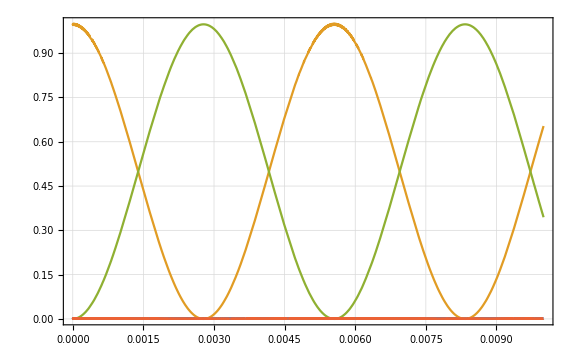

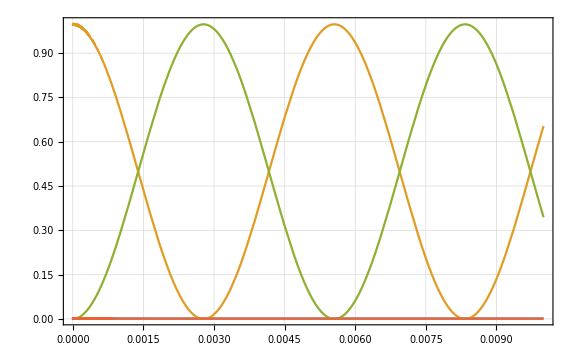

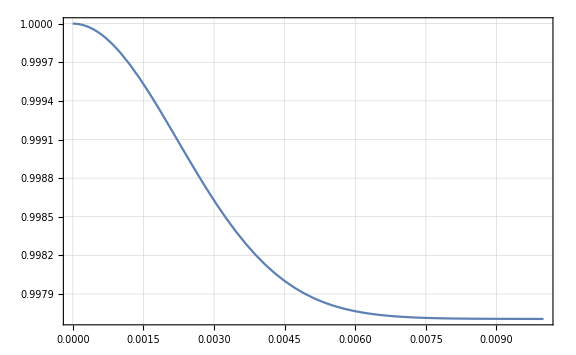

```mathematica
N0=.;
subParam={wB-> 11.3,Vt->11.4,ϵ->0,wcav-> 10.808452405257746, g->0.05 };
psisys0={{Subscript[α, 0,0],Subscript[α, 0,1],Subscript[α, 1,0],Subscript[α, 1,1]}};
rhocav0={1,1,1,1,1,1}; (* Assumption that rhocav is diagonal *)
rhocav0=rhocav0/Total[rhocav0];
nmin=0;nmax=Length@rhocav0-1;
Nmin=nmin;Nmax=nmax+2;
rhosys0=KroneckerProduct[Transpose[psisys0],psisys0];
rho0=Table[({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}),{n,1,Nmax+1}];
For[n=nmin,n<=nmax,n++,
rho0[[n+1]]+=({{1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})*rhocav0[[n+1]]*rhosys0;
rho0[[n+2]]+=({{0, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 0}})*rhocav0[[n+1]]*rhosys0;
rho0[[n+3]]+=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 1}})*rhocav0[[n+1]]*rhosys0;
]
Tmax=0.01;
(* Make sure |α|=1 and Sum[β]==1 *)
(*subNum={δ-> δf-(2 gc^2)/δc,δf-> wf-wcav,δc-> wc-wcav,wf->10.79,wc->11.4,wcav->10.808452405257746,gc->0.05,gf->0.005,wxy-> 0.002,wz->0,Subscript[α, 0,0]->0,Subscript[α, 0,1]->1,Subscript[α, 1,0]->0,Subscript[α, 1,1]->0,Subscript[β, 0]->1/2,Subscript[β, 1]->1/2};*)
ρt=Sum[ρNumerical[rho0[[N0+1]],H[N0],h[N0],Join[subAll,subParam],Tmax],{N0,Nmin,Nmax}];
Plot[Evaluate@Diagonal[ρt[[1,;;,;;]]],{t,0,Tmax},PlotRange->{0,1},Frame->True,GridLines->Automatic,ImageSize->Large]
Plot[Evaluate@Diagonal[ρt[[2,;;,;;]]],{t,0,Tmax},PlotRange->{0,1},Frame->True,GridLines->Automatic,ImageSize->Large]
Ft=Sum[Envelope[rho0[[N0+1]],H[N0],h[N0],Join[subAll,subParam],Tmax],{N0,Nmin,Nmax}];
Plot[Ft[[2,2]],{t,0,Tmax},Frame->True,GridLines->Automatic,ImageSize->Large]
```

```mathematica
Fenv[x_,y_]:=Sum[Envelope[rho0[[N0+1]],H[N0],h[N0],Join[subAll,{wB-> y,Vt->11.4,ϵ->x,wcav-> 10.808452405257746, g->0.05}],Tmax],{N0,Nmin,Nmax}][[2,2]]
GetDecTime[f_,target_:Exp[-1]]:=Return[t/.Solve[(f-Limit[f,t->∞])/Limit[f-Limit[f,t->∞],t->0]==target,t,Reals][[1]]]
DensityPlot[
GetDecTime[Fenv[x,y],0.99]
,{x,-1,10},{y,10,12},
ScalingFunctions->"Log10",ColorFunction->"SunsetColors",
Frame->True,FrameLabel->{"ϵ/2π (GHz)","ω_B/2π (GHz)"},
PlotLegends->Placed[Automatic,Below,Labeled[#,"T (ms)"]&],
ImageSize->Large
]
```

$Aborted

## Coupling Strength

```mathematica
Manipulate[
DensityPlot[
Abs[1000*1/2*g*z31*√N0]//.subZ//.subDef//.subNum//.{Vt->11.4,ϵ->x,wB->y},{x,-1,10},{y,10,12},
ScalingFunctions->"Log10",ColorFunction->"SunsetColors",
Frame->True,FrameLabel->{"ϵ/2π (GHz)","ω_B/2π (GHz)"},
PlotLegends->Placed[Automatic,Below,Labeled[#,"g_f/2π (MHz)"]&],
ImageSize->Large,
PlotPoints->25
]
,
{{N0,2},0,10},{{g,0.05},0,0.1}]
```

```mathematica
Manipulate[
DensityPlot[
Abs[1000*(E1-E0)]//.subE//.subZ//.subDef//.subNum//.{Vt->11.4,ϵ->x,wB->y},{x,-1,10},{y,10,12},
ScalingFunctions->"Log10",ColorFunction->"SunsetColors",
Frame->True,FrameLabel->{"ϵ/2π (GHz)","ω_B/2π (GHz)"},
PlotLegends->Placed[Automatic,Below,Labeled[#,"ω_ff/2π (MHz)"]&],
ImageSize->Large,
PlotPoints->25
]
,
{{N0,2},0,10},{{g,0.05},0,0.1}]
```

```mathematica
Manipulate[
DensityPlot[
Abs[1000*(E1-E0-wcav+(2*1/4*g^2*z10^2)/(E2-E0-wcav))]//.subE//.subZ//.subDef//.subNum//.{Vt->11.4,ϵ->x,wB->y},{x,-1,10},{y,10,12},
ScalingFunctions->"Log10",ColorFunction->"SunsetColors",
Frame->True,FrameLabel->{"ϵ/2π (GHz)","ω_B/2π (GHz)"},
PlotLegends->Placed[Automatic,Below,Labeled[#,"δ/2π (MHz)"]&],
ImageSize->Large,
PlotPoints->25
]
,
{{N0,2},0,10},{{g,0.05},0,0.1}]
```

ReplaceRepeated::reps: {subE} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {subZ} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {subDef} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

ReplaceRepeated::reps: {subE} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {subZ} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {subDef} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

```mathematica
Manipulate[
DensityPlot[
Abs[(E2-E1)]//.subE//.subZ//.subDef//.subNum//.{Vt->11.4,ϵ->x,wB->y},{x,-1,10},{y,10,12},
ScalingFunctions->"Log10",ColorFunction->"SunsetColors",
Frame->True,FrameLabel->{"ϵ/2π (GHz)","ω_B/2π (GHz)"},
PlotLegends->Placed[Automatic,Below,Labeled[#,"E2-E1 (GHz)"]&],
ImageSize->Large,
PlotPoints->50
]
,
{{N0,2},0,10},{{g,0.05},0,0.1}]
```

```mathematica
Manipulate[
DensityPlot[
Abs[Δ[N0]]//.{gf-> 1/2*g*z31,δ->E1-E0-wcav+(2*1/4*g^2*z10^2)/(E2-E0-wcav) }//.subE//.subZ//.subDef//.subNum//.{Vt->11.4,ϵ->x,wB->y},{x,-1,10},{y,10,12},
ScalingFunctions->"Log10",ColorFunction->"SunsetColors",
Frame->True,FrameLabel->{"ϵ/2π (GHz)","ω_B/2π (GHz)"},
PlotLegends->Placed[Automatic,Below,Labeled[#,"gf/δ"]&],
ImageSize->Large,
PlotPoints->25
]
,
{{N0,2},0,10},{{g,0.05},0,0.1}]
```

ReplaceRepeated::reps: {subE} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {subZ} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {subDef} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

ReplaceRepeated::reps: {subE} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {subZ} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceRepeated::reps: {subDef} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceRepeated::reps will be suppressed during this calculation.

### Calculating the Decoherence Time

```mathematica
GetDecTime[f_,target_:Exp[-1]]:=Return[t/.Solve[(f-Limit[f,t->∞])/Limit[f-Limit[f,t->∞],t->0]==target,t,Reals][[1]]]
```

{{1,0,0,0},{0,1/(√2),1/(√2),0},{0,-1/(√2),1/(√2),0},{0,0,0,1}}

{{{0,0,0.+1.79539×10^-6 ⅈ,0},{0,0,0,0},{0.+1.79539×10^-6 ⅈ,0,-0.000513925,0},{0,0,0,-0.000513925}},{{0,0.+1.79539×10^-6 ⅈ,0,0},{0.+1.79539×10^-6 ⅈ,-0.000513925,0,0},{0,0,0,0},{0,0,0,-0.000513925}}}

{{0.994064,0,-0.108957,0},{0.0770445,1/(√2),0.702909,0},{0.0770445,-1/(√2),0.702909,0},{0,0,0,1}}

{{{0,0,1.79539×10^-6,0},{0,0,0,0},{1.79539×10^-6,0,-0.000513925,0},{0,0,0,-0.000513925}},{{0,1.79539×10^-6,0,0},{1.79539×10^-6,-0.000513925,0,0},{0,0,0,0},{0,0,0,-0.000513925}}}

{{0.988128,0,-0.154089,0.00839457},{0.108957,1/(√2),0.694515,-0.0770445},{0.108957,-1/(√2),0.694515,-0.0770445},{0.00839457,0,0.108957,0.994064}}

{{{0,0,2.53906×10^-6,0},{0,0,0,1.79539×10^-6},{2.53906×10^-6,0,-0.000513925,0},{0,1.79539×10^-6,0,-0.000513925}},{{0,2.53906×10^-6,0,0},{2.53906×10^-6,-0.000513925,0,0},{0,0,0,1.79539×10^-6},{0,0,1.79539×10^-6,-0.000513925}}}

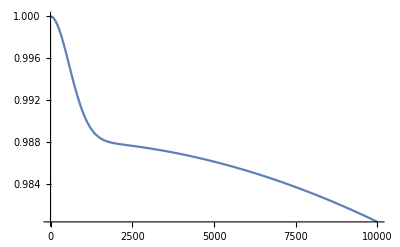

```mathematica
(* Make sure |α|=1 and Sum[β]==1 *)
Ft=Sum[Envelope[rho0[[N0+1]],H[N0],h[N0],R[N0],Join[subAll,subParam],Tmax],{N0,Nmin,Nmax}];
Plot[Ft[[2,2]],{t,0,Tmax}]
```

```mathematica
H[3]//.Join[subAll,subParam]
```

{{0.0225506,0.00300927,0.00300927,0},{0.00300927,0,0,0.00245706},{0.00300927,0,0,0.00245706},{0,0.00245706,0.00245706,-0.0225506}}

```mathematica
Envelope[rho0[[1+1]],H[1],h[1],R[1],Join[subAll,subParam],Tmax]
```

{{0.994064,0,-0.108957,0},{0.0770445,1/(√2),0.702909,0},{0.0770445,-1/(√2),0.702909,0},{0,0,0,1}}

{{{0,0,1.79539×10^-6,0},{0,0,0,0},{1.79539×10^-6,0,0.000256962,0},{0,0,0,0.000256962}},{{0,1.79539×10^-6,0,0},{1.79539×10^-6,0.000256962,0,0},{0,0,0,0},{0,0,0,0.000256962}}}

{{0.00586518+4.20426×10^-19 ⅇ^(-1.83432×10^-8 t^2 (2-EulerGamma-Log[(π t)/500000000000]))-0.00586518 ⅇ^(-1.78256×10^-8 t^2 (2-EulerGamma-Log[(π t)/500000000000]))-4.20426×10^-19 ⅇ^(-3.70435×10^-12 t^2 (2-EulerGamma-Log[(π t)/500000000000])),-0.0186915+0.0191461 ⅇ^(-1.83432×10^-8 t^2 (2-EulerGamma-Log[(π t)/500000000000]))+0.0186915 ⅇ^(-1.78256×10^-8 t^2 (2-EulerGamma-Log[(π t)/500000000000]))-0.0191461 ⅇ^(-3.70435×10^-12 t^2 (2-EulerGamma-Log[(π t)/500000000000])),-0.0186915-0.0191461 ⅇ^(-1.83432×10^-8 t^2 (2-EulerGamma-Log[(π t)/500000000000]))+0.0186915 ⅇ^(-1.78256×10^-8 t^2 (2-EulerGamma-Log[(π t)/500000000000]))+0.0191461 ⅇ^(-3.70435×10^-12 t^2 (2-EulerGamma-Log[(π t)/500000000000])),0.},{-0.0186915+0.0191461 ⅇ^(-1.83432×10^-8 t^2 (2-EulerGamma-Log[(π t)/500000000000]))+0.0186915 ⅇ^(-1.78256×10^-8 t^2 (2-EulerGamma-Log[(π t)/500000000000]))-0.0191461 ⅇ^(-3.70435×10^-12 t^2 (2-EulerGamma-Log[(π t)/500000000000])),0.247067+0.00296782 ⅇ^(-1.83432×10^-8 t^2 (2-EulerGamma-Log[(π t)/500000000000]))+0.00293259 ⅇ^(-1.78256×10^-8 t^2 (2-EulerGamma-Log[(π t)/500000000000]))+0.247032 ⅇ^(-3.70435×10^-12 t^2 (2-EulerGamma-Log[(π t)/500000000000])),-0.00293259-6.50521×10^-19 ⅇ^(-1.83432×10^-8 t^2 (2-EulerGamma-Log[(π t)/500000000000]))+0.00293259 ⅇ^(-1.78256×10^-8 t^2 (2-EulerGamma-Log[(π t)/500000000000]))-4.16334×10^-17 ⅇ^(-3.70435×10^-12 t^2 (2-EulerGamma-Log[(π t)/500000000000])),0.},{-0.0186915-0.0191461 ⅇ^(-1.83432×10^-8 t^2 (2-EulerGamma-Log[(π t)/500000000000]))+0.0186915 ⅇ^(-1.78256×10^-8 t^2 (2-EulerGamma-Log[(π t)/500000000000]))+0.0191461 ⅇ^(-3.70435×10^-12 t^2 (2-EulerGamma-Log[(π t)/500000000000])),-0.00293259+0.00293259 ⅇ^(-1.78256×10^-8 t^2 (2-EulerGamma-Log[(π t)/500000000000])),0.247067-0.00296782 ⅇ^(-1.83432×10^-8 t^2 (2-EulerGamma-Log[(π t)/500000000000]))+0.00293259 ⅇ^(-1.78256×10^-8 t^2 (2-EulerGamma-Log[(π t)/500000000000]))-0.247032 ⅇ^(-3.70435×10^-12 t^2 (2-EulerGamma-Log[(π t)/500000000000])),0.},{0.,0.,0.,0.}}

∞

```mathematica
Ft[[2,2]]
```

(0.488413+0. ⅈ)+0.0000704241 ⅇ^(-7.83938×10^-13 t^2 (2-EulerGamma-Log[(π t)/500000000000]))+0.0057227 ⅇ^(-7.71445×10^-13 t^2 (2-EulerGamma-Log[(π t)/500000000000]))+0.00293259 ⅇ^(-3.45756×10^-13 t^2 (2-EulerGamma-Log[(π t)/500000000000]))+0.00593397 ⅇ^(-3.45635×10^-13 t^2 (2-EulerGamma-Log[(π t)/500000000000]))+0.00296699 ⅇ^(-8.85033×10^-14 t^2 (2-EulerGamma-Log[(π t)/500000000000]))+0.247032 ⅇ^(-8.64391×10^-14 t^2 (2-EulerGamma-Log[(π t)/500000000000]))+0.00296782 ⅇ^(-8.64391×10^-14 t^2 (2-EulerGamma-Log[(π t)/500000000000]))+0.241099 ⅇ^(-8.43393×10^-14 t^2 (2-EulerGamma-Log[(π t)/500000000000]))+0.00286135 ⅇ^(-5.01675×10^-17 t^2 (2-EulerGamma-Log[(π t)/500000000000]))